```mathematica
A:=({{-3, 2, 1}, {0, 2, 2}, {0, -1, -1}})
```

```mathematica
Eigenvalues[A]
```

{-3,1,0}

```mathematica
Eigenvectors[A]
```

{{1,0,0},{-3,-8,4},{-1,-3,3}}

```mathematica
R:=({{Cos[t], -Sin[t]}, {Sin[t], Cos[t]}})
```

```mathematica
Eigenvalues[R]
```

{Cos[t]-ⅈ Sin[t],Cos[t]+ⅈ Sin[t]}

```mathematica
Eigenvectors[R]
```

{{-ⅈ,1},{ⅈ,1}}

```mathematica
B := ({{0, 0, 1}, {0, -1, 0}, {1, 0, 0}})
```

```mathematica
Eigenvalues[B]
```

{-1,-1,1}

```mathematica
Eigenvectors[B]
```

{{-1,0,1},{0,1,0},{1,0,1}}

```mathematica
F:=({{3, -1}, {-1, 3}})
```

```mathematica
Eigenvalues[F]
```

{4,2}

```mathematica
Eigenvectors[F]
```

{{-1,1},{1,1}}

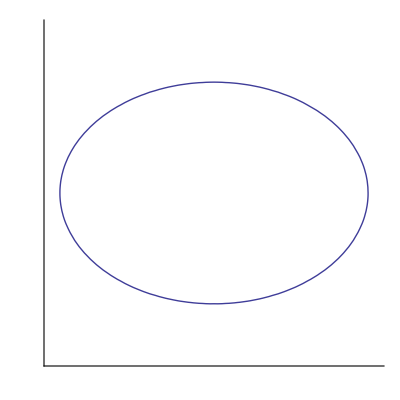

```mathematica
ContourPlot[u^2/2+v^2==1,{u, -3/2,3/2},{v, -3/2,3/2},Frame->None,Axes->True,Ticks->None]
```

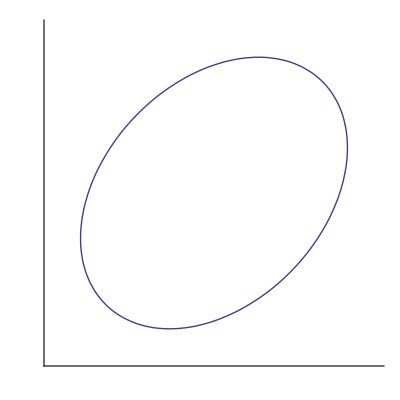

```mathematica
ContourPlot[3 x^2-2x y+3 y^2==4,{x, -3/2,3/2},{y, -3/2,3/2},Frame->None,Axes->True,Ticks->None]
```

```mathematica
∫_-1^1 (3/2 √(5/2)x^2-1/2 √(5/2))^2 ⅆx
```

1

```mathematica
Manipulate[Show[ContourPlot3D[{ a x+b y+c z==0,p x+q y+r z==0,(b r-c q)x+(c p-a r)y+(a q-b p)z==0},{x,-R,R},{y,-R,R},{z,-R,R},Mesh->None,ContourStyle->{RGBColor[100/255,200/255,150/255],RGBColor[100/255,200/255,150/255],RGBColor[0,0,0.8]},Boxed->False],ContourPlot3D[z==1,{x,-R,R},{y,-R,R},{z,-R,R},ContourStyle->{Opacity[X]},MeshStyle->None,Boxed->False],ParametricPlot3D[{{t(b r -c q),t(c p-a r),t(a q-b p)},{t a , t b, t c},{t p , t q, t r}},{t,-3,3},PlotStyle->{Thick},Boxed->False],ParametricPlot3D[{{(-c q+b r)/(a q-b p)+b t,(-a r+c p)/(a q-b p)-a t,1},{(-c q+b r)/(a q-b p)+q t,(-a r+c p)/(a q-b p)-p t,1},{(-c (c p-a r)+b (a q-b p))/(a (c p-a r)-b (b r-c q))+(c p-a r) t,(-a (a q-b p)+c (b r-c q))/(a (c p-a r)-b (b r-c q))-(b r-c q) t,1}},{t,-3,3},PlotStyle->RGBColor[1,1,0],Boxed->False]],{a,1,2},{b,1,2},{c,1,2},{p,1,2},{q,-1,-2},{r,1,2},{X,0.1,0.9},{R,1.7,3}]
```